{-0.199937,0.199937}

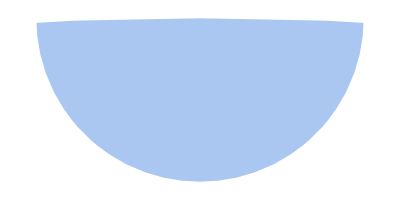

0.0621644

```mathematica
a=2;
b=1;
mu=0.2;

x0 = 0;
y0 = 1;

ellipse[x_] = b*Sqrt[1-(x/a)^2];
circle[x_] = - Sqrt[mu^2-(x-x0)^2] + y0;

sol = x/.Solve[ellipse[x] == circle[x], x];
Print[sol];

ellipseDisk = Disk[{0, 0},{a, b}];
circleDisk = Disk[{x0, y0}, mu];

R = RegionIntersection[ellipseDisk, circleDisk];

Region[R]
N[Area[R]]
```

```mathematica
areaEllipse[x_] = Integrate[ellipse[x], x];
areaCircle[x_] = Integrate[circle[x], x];

difference[x_] = areaEllipse[x] - areaCircle[x];

res = difference[sol[[2]]] - difference[sol[[1]]];

N[areaEllipse[sol[[2]]] - areaEllipse[sol[[1]]]]
N[areaCircle[sol[[2]]] - areaCircle[sol[[1]]]]
N[res]
```

0.399207

0.337043

0.0621644

```mathematica
Solve[{
(x1-cx)^2+(y1-cy)^2 == mu^2,
 (x2-cx)^2 + (y2-cy)^2==mu^2,
 (x1/a)^2 + (y1/b)^2 == 1,
(x1-x0)*(x1-cx) + (y1-y0)*(y1-cy)==0}, {cx, cy, x1, y1}]
```

```mathematica
res = Solve[{(x1-x0)(mux-x1)+(y1-y0)(muy-y1)==0,(mux-x1)^2 + (muy-y1)^2 == mu^2} , {mux, muy}];
Simplify[res]
```

{{mux→(x0^2 x1-2 x0 x1^2+x1^3+x1 (y0-y1)^2-√(mu^2 (x0^2-2 x0 x1+x1^2+(y0-y1)^2) (y0-y1)^2))/(x0^2-2 x0 x1+x1^2+(y0-y1)^2),muy→(-x1 √(mu^2 (x0^2-2 x0 x1+x1^2+(y0-y1)^2) (y0-y1)^2)+x0^2 (y0-y1) y1+x1^2 (y0-y1) y1+(y0-y1)^3 y1+x0 (√(mu^2 (x0^2-2 x0 x1+x1^2+(y0-y1)^2) (y0-y1)^2)+2 x1 y1 (-y0+y1)))/((x0^2-2 x0 x1+x1^2+(y0-y1)^2) (y0-y1))},{mux→(x0^2 x1-2 x0 x1^2+x1^3+x1 (y0-y1)^2+√(mu^2 (x0^2-2 x0 x1+x1^2+(y0-y1)^2) (y0-y1)^2))/(x0^2-2 x0 x1+x1^2+(y0-y1)^2),muy→(x1 √(mu^2 (x0^2-2 x0 x1+x1^2+(y0-y1)^2) (y0-y1)^2)+x0^2 (y0-y1) y1+x1^2 (y0-y1) y1+(y0-y1)^3 y1-x0 (√(mu^2 (x0^2-2 x0 x1+x1^2+(y0-y1)^2) (y0-y1)^2)+2 x1 (y0-y1) y1))/((x0^2-2 x0 x1+x1^2+(y0-y1)^2) (y0-y1))}}

```mathematica
res = Reduce[
{
(x-x0)^2 + (y-y0)^2 - mu^2 == 0,
(x/a)^2 + (y/b)^2 - 1 == 0
},
{x, y}, Reals];
Simplify[res]
```

Root::rnum: x is not a valid root number.

```mathematica
a4 = a^2*(y0^2-b^2) + b^2(x0-mu)^2;
a3 = 4*a^2*mu*y0;
a2 = 2*(a^2*(y0^2 - b^2 + 2*mu^2) + b^2*(x0^2 - mu^2));
a1 = 4*a^2*mu*y0;
a0 = a^2 * (y0^2 - b^2) + b^2(x0 - mu)^2;
Roots[
a4*z^4 + a3*z^3 + a2*z^2 + a1*z + a0 ==0, z
]
```

z==-(a^2 mu y0)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)-1/2 √((4 a^4 mu^2 y0^2)/((-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)^2)-(4 a^2 mu^2)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)+(4 b^2 mu^2)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)-(4 b^2 mu x0)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2))-1/2 √((8 a^4 mu^2 y0^2)/((-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)^2)+(2 (a^2 b^2-2 a^2 mu^2+b^2 mu^2-b^2 x0^2-a^2 y0^2))/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)-(-2 a^2 b^2+2 b^2 mu^2-4 b^2 mu x0+2 b^2 x0^2+2 a^2 y0^2)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)-(-(64 a^6 mu^3 y0^3)/((-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)^3)-(32 a^2 mu y0 (a^2 b^2-2 a^2 mu^2+b^2 mu^2-b^2 x0^2-a^2 y0^2))/((-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)^2)-(32 a^2 mu y0)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2))/(4 √((4 a^4 mu^2 y0^2)/((-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)^2)-(4 a^2 mu^2)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)+(4 b^2 mu^2)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)-(4 b^2 mu x0)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2))))||z==-(a^2 mu y0)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)-1/2 √((4 a^4 mu^2 y0^2)/((-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)^2)-(4 a^2 mu^2)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)+(4 b^2 mu^2)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)-(4 b^2 mu x0)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2))+1/2 √((8 a^4 mu^2 y0^2)/((-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)^2)+(2 (a^2 b^2-2 a^2 mu^2+b^2 mu^2-b^2 x0^2-a^2 y0^2))/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)-(-2 a^2 b^2+2 b^2 mu^2-4 b^2 mu x0+2 b^2 x0^2+2 a^2 y0^2)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)-(-(64 a^6 mu^3 y0^3)/((-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)^3)-(32 a^2 mu y0 (a^2 b^2-2 a^2 mu^2+b^2 mu^2-b^2 x0^2-a^2 y0^2))/((-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)^2)-(32 a^2 mu y0)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2))/(4 √((4 a^4 mu^2 y0^2)/((-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)^2)-(4 a^2 mu^2)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)+(4 b^2 mu^2)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)-(4 b^2 mu x0)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2))))||z==-(a^2 mu y0)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)+1/2 √((4 a^4 mu^2 y0^2)/((-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)^2)-(4 a^2 mu^2)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)+(4 b^2 mu^2)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)-(4 b^2 mu x0)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2))-1/2 √((8 a^4 mu^2 y0^2)/((-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)^2)+(2 (a^2 b^2-2 a^2 mu^2+b^2 mu^2-b^2 x0^2-a^2 y0^2))/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)-(-2 a^2 b^2+2 b^2 mu^2-4 b^2 mu x0+2 b^2 x0^2+2 a^2 y0^2)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)+(-(64 a^6 mu^3 y0^3)/((-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)^3)-(32 a^2 mu y0 (a^2 b^2-2 a^2 mu^2+b^2 mu^2-b^2 x0^2-a^2 y0^2))/((-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)^2)-(32 a^2 mu y0)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2))/(4 √((4 a^4 mu^2 y0^2)/((-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)^2)-(4 a^2 mu^2)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)+(4 b^2 mu^2)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)-(4 b^2 mu x0)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2))))||z==-(a^2 mu y0)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)+1/2 √((4 a^4 mu^2 y0^2)/((-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)^2)-(4 a^2 mu^2)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)+(4 b^2 mu^2)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)-(4 b^2 mu x0)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2))+1/2 √((8 a^4 mu^2 y0^2)/((-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)^2)+(2 (a^2 b^2-2 a^2 mu^2+b^2 mu^2-b^2 x0^2-a^2 y0^2))/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)-(-2 a^2 b^2+2 b^2 mu^2-4 b^2 mu x0+2 b^2 x0^2+2 a^2 y0^2)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)+(-(64 a^6 mu^3 y0^3)/((-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)^3)-(32 a^2 mu y0 (a^2 b^2-2 a^2 mu^2+b^2 mu^2-b^2 x0^2-a^2 y0^2))/((-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)^2)-(32 a^2 mu y0)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2))/(4 √((4 a^4 mu^2 y0^2)/((-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)^2)-(4 a^2 mu^2)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)+(4 b^2 mu^2)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2)-(4 b^2 mu x0)/(-a^2 b^2+b^2 mu^2-2 b^2 mu x0+b^2 x0^2+a^2 y0^2))))

```mathematica
dist[z_, cx_, cy_] = ((cx + R*(1-z^2)/(1+z^2))/a)^2 + ((cy+R(2z)/(1+z^2))/b)^2;
point[z_, cx_, cy_] = {(cx + R*(1-z^2)/(1+z^2)), (cy+R(2z)/(1+z^2))};

dist[z1, cx, cy]
dist[z2, cx, cy]
point[z2, cx, cy]

Solve[
{
dist[z1, cx, cy] == 1,
dist[z2, cx, cy] == 1,
point[z2, cx, cy] == {x2, y2}
},
{z1, z2, cx, cy}, Reals]
```

```mathematica
z1 = Solve[((cx + R*(1-z^2)/(1+z^2))/a)^2 + ((cy+R(2z)/(1+z^2))/b)^2 ==1, z];
```

```mathematica
cximpl = Solve[(x2-cx)^2 + (y2-cy)^2 == mu^2, cx];
z1next = z1/.cximpl;

x1 = cx + (1-z/.z1next)^2/(1+z/.z1next)^2;
y1 = cy + 2*(z/.z1next)/(1+(z/.z1next))^2;

text = (x1 - x0)*(x1-cx) + (y1-y0)*(y1-muy);
Dimensions[text]
text

res = Solve[test == 0, cy];
res
```

{2,4}

{}

```mathematica
(*Solve[(x1 - x0)*(x1-cx) + (y1-y0)*(y1-muy) == 0, cx]*)
```

```mathematica
z1 = Solve[(cx + R*Cos[z])^2 + (cy+R*Sin[z])^2 ==1, z];
```

```mathematica
center[zc_] = {x2, y2} + R*{(1-zc)^2/(1+zc^2), 2zc/(1+zc)^2};

a4[zc_] = a^2*(center[zc][[2]]-b^2) + b^2(center[zc][[1]]-mu)^2;
a3[zc_] = 4*a^2*mu*center[zc][[2]];
a2[zc_] = 2*(a^2*(center[zc][[2]]^2 - b^2 + 2*mu^2) + b^2*(center[zc][[1]]^2 - mu^2));
a1[zc_] = 4*a^2*mu*center[zc][[2]];
a0[zc_] = a^2 * (center[zc][[2]]^2 - b^2) + b^2(center[zc][[1]] - mu)^2;
```

```mathematica
intersections = Roots[
a4[zc]*z^4 + a3[zc]*z^3 + a2[zc]*z^2 + a1[zc]*z + a0[zc] ==0, z
];
```

```mathematica
ToRadicals[intersections[[1]]]
```

```mathematica
intersectiontangents = {-4z/(1+z)^2, 2(1-z)^2/(1+z)^2}/.intersections
```

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.